## Initialization

```mathematica
(*Import FeynCalc Package*)
```

```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
(*Clear Variables and Scalar Products*)
```

```mathematica
ClearAll["Global`*"];
ClearScalarProducts;
```

## Compton Tensor

```mathematica
ϵt[a_,b_]:=(Sqrt[2]*Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]])/(-Sqrt[Contract[Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]]*Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]]]]);
gt[a_,b_]:=Contract[ϵt[a,c]*ϵt[b,c]];

𝒯1[a_,b_]:=-1/2 gt[a,b];
𝒯1t[a_,b_]:=ⅈ/2 ϵt[a,b];
```

## DVCS Leptonic Tensor

```mathematica
(LDVCSunp=Simplify[DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].(GA[α1]/Q^2).SpinorU[k]]*SpinorUBar[kp].(GA[α2]/Q^2).SpinorU[k]]],{h^2==1}]) //TraditionalForm
(LDVCSp=Simplify[-ⅈ*DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].(GA[α1]/Q^2).SpinorU[k]]*SpinorUBar[kp].(GA[α2]/Q^2).DiracMatrix[5].SpinorU[k]]],{h^2==1}]) //TraditionalForm
```

(2 (-(ḡ)^α1α2 (k̄·OverBar[kp])+(k̄)^α2 OverBar[kp]^α1+(k̄)^α1 OverBar[kp]^α2))/Q^4

(2 (ϵ̄)^(α1α2 k̄ OverBar[kp]))/Q^4

## DVCS Scalar Coefficients

```mathematica
(hampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1[α3,α1]]*𝒯1[α4,α2]*(-MT[α3,α4])]]]) //TraditionalForm
(htampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1t[α3,α1]]*𝒯1t[α4,α2]*(-MT[α3,α4])]]]) //TraditionalForm
(hplusampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]+𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]]) //TraditionalForm
(hminusampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]-𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]]) //TraditionalForm
```

((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

0

((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp]))/(√((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

## Interference Leptonic Tensor

```mathematica
(LINTunp=Expand[Simplify[DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].GA[α2].SpinorU[k]]*Contract[SpinorUBar[kp].(GA[α1].((GS[kp]+GS[qp])/(2 SP[kp,qp])).GA[α]+GA[α].((GS[k]-GS[qp])/(-2SP[k,qp])).GA[α1]).SpinorU[k]]]]]]) //TraditionalForm;
(LINTp=Expand[Simplify[-ⅈ*DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].GA[α2].SpinorU[k]]*Contract[SpinorUBar[kp].(GA[α1].((GS[kp]+GS[qp])/(2 SP[kp,qp])).GA[α]+GA[α].((GS[k]-GS[qp])/(-2SP[k,qp])).GA[α1]).DiracMatrix[5].SpinorU[k]]]]]]) //TraditionalForm;
```

## Interference scalar coefficients

```mathematica
(AINTunpc=Simplify[ScalarProductExpand[Contract[8*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]) //TraditionalForm
(BINTunpc=Simplify[ScalarProductExpand[Contract[2*t*FV[n,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]) //TraditionalForm
(CINTunpc=Simplify[ScalarProductExpand[Contract[4 ⅈ *Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]) //TraditionalForm

(AtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(BtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(CtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4*Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm

(AINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*FV[p,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(BINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*t*FV[n,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(CINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4 ⅈ *Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm

(AtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*FV[p,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(BtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(CtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4*Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
```

1/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))8 (2 (p̄·q̄) (q̄·OverBar[qp]) (k̄·OverBar[qp])^3-(k̄·OverBar[qp])^2 (-2 (k̄·p̄) ((q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄·OverBar[qp])^2)+2 (k̄·q̄) ((p̄·OverBar[qp]) (q̄·OverBar[qp])+OverBar[qp]^2 (p̄·q̄))+(q̄·OverBar[qp]) ((p̄·q̄) (2 (q̄·OverBar[qp])+(q̄)^2)-(q̄)^2 (p̄·OverBar[qp])))+(k̄·OverBar[qp]) (2 (k̄·p̄) (q̄·OverBar[qp])^3-(q̄)^2 (k̄·p̄) (q̄·OverBar[qp])^2+2 OverBar[qp]^2 (p̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (k̄·p̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)+(p̄·OverBar[qp]) (2 (q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-2 OverBar[qp]^2))+(p̄·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]+2 OverBar[qp]^2))-(q̄)^2 (p̄·OverBar[qp]) (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2 (k̄·p̄) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2 (k̄·p̄)+(k̄)^2 (q̄)^2 (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 OverBar[qp]^2 (p̄·q̄) (q̄·OverBar[qp]))-(k̄·q̄) (q̄·OverBar[qp]) (-(k̄·p̄) (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2 (k̄·p̄)+(k̄)^2 (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))+(k̄·q̄) ((p̄·OverBar[qp]) (q̄·OverBar[qp]+OverBar[qp]^2)-2 OverBar[qp]^2 (k̄·p̄))+OverBar[qp]^2 (p̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2 (p̄·OverBar[qp])))

1/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))2 t (2 (n̄·q̄) (q̄·OverBar[qp]) (k̄·OverBar[qp])^3-(k̄·OverBar[qp])^2 (-2 (k̄·n̄) ((q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄·OverBar[qp])^2)+2 (k̄·q̄) ((n̄·OverBar[qp]) (q̄·OverBar[qp])+OverBar[qp]^2 (n̄·q̄))+(q̄·OverBar[qp]) ((n̄·q̄) (2 (q̄·OverBar[qp])+(q̄)^2)-(q̄)^2 (n̄·OverBar[qp])))+(k̄·OverBar[qp]) (2 (k̄·n̄) (q̄·OverBar[qp])^3-(q̄)^2 (k̄·n̄) (q̄·OverBar[qp])^2+2 OverBar[qp]^2 (n̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (k̄·n̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)+(n̄·OverBar[qp]) (2 (q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-2 OverBar[qp]^2))+(n̄·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]+2 OverBar[qp]^2))-(q̄)^2 (n̄·OverBar[qp]) (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2 (k̄·n̄) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2 (k̄·n̄)+(k̄)^2 (q̄)^2 (OverBar[qp]^2 (n̄·q̄)-(n̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 OverBar[qp]^2 (n̄·q̄) (q̄·OverBar[qp]))-(k̄·q̄) (q̄·OverBar[qp]) (-(k̄·n̄) (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2 (k̄·n̄)+(k̄)^2 (OverBar[qp]^2 (n̄·q̄)-(n̄·OverBar[qp]) (q̄·OverBar[qp]))+(k̄·q̄) ((n̄·OverBar[qp]) (q̄·OverBar[qp]+OverBar[qp]^2)-2 OverBar[qp]^2 (k̄·n̄))+OverBar[qp]^2 (n̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2 (n̄·OverBar[qp])))

(4 ((k̄·q̄) (2 (k̄·OverBar[qp])-q̄·OverBar[qp])-(k̄·OverBar[qp]) (2 (k̄·OverBar[qp])-2 (q̄·OverBar[qp])+(q̄)^2)) ((k̄·OverBar[pp]) ((n̄·OverBar[qp]) (p̄·q̄)-(n̄·q̄) (p̄·OverBar[qp]))+(k̄·p̄) ((n̄·q̄) (OverBar[pp]·OverBar[qp])-(n̄·OverBar[qp]) (OverBar[pp]·q̄))+(k̄·n̄) ((p̄·OverBar[qp]) (OverBar[pp]·q̄)-(p̄·q̄) (OverBar[pp]·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(8 ((k̄·OverBar[qp]) (2 (k̄·OverBar[qp])-2 (q̄·OverBar[qp])+(q̄)^2)+(k̄·q̄) (q̄·OverBar[qp]-2 (k̄·OverBar[qp]))) (ϵ̄)^(k̄ p̄ q̄ OverBar[qp]))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(2 t ((k̄·OverBar[qp]) (2 (k̄·OverBar[qp])-2 (q̄·OverBar[qp])+(q̄)^2)+(k̄·q̄) (q̄·OverBar[qp]-2 (k̄·OverBar[qp]))) (ϵ̄)^(k̄ n̄ q̄ OverBar[qp]))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

1/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))4 ((ϵ̄)^(n̄ p̄ OverBar[pp]q̄) (-2 (q̄·OverBar[qp]) (k̄·OverBar[qp])^3+(k̄·OverBar[qp])^2 (2 ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄))+(q̄)^2 (q̄·OverBar[qp]))-(k̄·OverBar[qp]) ((q̄)^2 OverBar[qp]^2 ((k̄)^2+q̄·OverBar[qp])+(k̄·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]+2 OverBar[qp]^2))+OverBar[qp]^2 (k̄·q̄) (q̄·OverBar[qp]) ((k̄)^2+q̄·OverBar[qp]))+(ϵ̄)^(n̄ p̄ OverBar[pp]OverBar[qp]) ((k̄·q̄)^2 ((q̄·OverBar[qp])^2-2 OverBar[qp]^2 (k̄·OverBar[qp])+OverBar[qp]^2 (q̄·OverBar[qp]))+(k̄·q̄) (2 (q̄·OverBar[qp]) (k̄·OverBar[qp])^2-(k̄·OverBar[qp]) (2 (q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-2 OverBar[qp]^2))-(q̄·OverBar[qp]) ((k̄)^2 (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2))+(q̄)^2 (k̄·OverBar[qp]) (q̄·OverBar[qp]) (-k̄·OverBar[qp]+(k̄)^2+q̄·OverBar[qp]))+(ϵ̄)^(k̄ n̄ p̄ OverBar[pp]) (2 (k̄·OverBar[qp])^2 ((q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄·OverBar[qp])^2)-(k̄·OverBar[qp]) (2 (k̄·q̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)-((q̄)^2-2 (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))+(k̄·q̄) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (2 (k̄·q̄)-(q̄)^2))))

-(8 (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])) (ϵ̄)^(k̄ p̄ q̄ OverBar[qp]))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

-(2 t (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])) (ϵ̄)^(k̄ n̄ q̄ OverBar[qp]))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

1/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))(-4 (ϵ̄)^(n̄ p̄ OverBar[pp]OverBar[qp]) ((q̄·OverBar[qp]-2 (k̄·OverBar[qp])) (k̄·q̄)^2+(q̄)^2 (k̄·q̄) (k̄·OverBar[qp])+(k̄)^2 ((k̄·q̄) (2 (k̄·OverBar[qp])-q̄·OverBar[qp])-(q̄)^2 (k̄·OverBar[qp]))+(q̄)^2 (k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]))+4 (ϵ̄)^(n̄ p̄ OverBar[pp]q̄) ((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) (-2 (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (q̄·OverBar[qp]+OverBar[qp]^2)-OverBar[qp]^2 (q̄·OverBar[qp]))+2 (k̄)^2 (k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]))+4 (q̄·OverBar[qp]+OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])) (ϵ̄)^(k̄ n̄ p̄ OverBar[pp]))

-1/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))8 ((p̄·OverBar[qp]) (2 (k̄·OverBar[qp])-q̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (p̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) ((p̄·q̄) (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄)^2 (p̄·OverBar[qp]))+(q̄·OverBar[qp]) ((k̄·p̄) (q̄·OverBar[qp]+OverBar[qp]^2)-OverBar[qp]^2 (p̄·q̄)))+(k̄)^2 (2 (p̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (-2 (k̄·q̄) (p̄·OverBar[qp])+(q̄)^2 (p̄·OverBar[qp])-2 (p̄·q̄) (q̄·OverBar[qp]))+(k̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 (k̄·OverBar[qp]) ((k̄·OverBar[qp]) (p̄·q̄-p̄·OverBar[qp])-(k̄·p̄) (q̄·OverBar[qp]+OverBar[qp]^2)+(p̄·OverBar[qp]) (q̄·OverBar[qp])))

-1/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))2 t ((n̄·OverBar[qp]) (2 (k̄·OverBar[qp])-q̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (n̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) ((n̄·q̄) (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄)^2 (n̄·OverBar[qp]))+(q̄·OverBar[qp]) ((k̄·n̄) (q̄·OverBar[qp]+OverBar[qp]^2)-OverBar[qp]^2 (n̄·q̄)))+(k̄)^2 (2 (n̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (-2 (k̄·q̄) (n̄·OverBar[qp])+(q̄)^2 (n̄·OverBar[qp])-2 (n̄·q̄) (q̄·OverBar[qp]))+(k̄·q̄) (n̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 (k̄·OverBar[qp]) ((k̄·OverBar[qp]) (n̄·q̄-n̄·OverBar[qp])-(k̄·n̄) (q̄·OverBar[qp]+OverBar[qp]^2)+(n̄·OverBar[qp]) (q̄·OverBar[qp])))

(4 (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])) ((k̄·OverBar[pp]) ((n̄·OverBar[qp]) (p̄·q̄)-(n̄·q̄) (p̄·OverBar[qp]))+(k̄·p̄) ((n̄·q̄) (OverBar[pp]·OverBar[qp])-(n̄·OverBar[qp]) (OverBar[pp]·q̄))+(k̄·n̄) ((p̄·OverBar[qp]) (OverBar[pp]·q̄)-(p̄·q̄) (OverBar[pp]·OverBar[qp]))))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

## Input of scalar productions and ϵ symbol to FeynCalc

```mathematica
SP[k,k]=SP[kp,kp]=SP[qp,qp]=0;
SP[p,p]=SP[pp,pp]=M^2;
SP[p,pp]= M^2-t/2;
SP[k,k]=SP[kp,kp]=SP[qp,qp]=0;
SP[q,q]=-Q^2;
SP[p,p]=SP[pp,pp]=M^2;
SP[k,kp]=Q^2/2;
SP[q,qp]=-(Q^2+t)/2;
SP[p,pp]= M^2-t/2;
SP[k,q]=-Q^2/2;
SP[kp,q]=Q^2/2;
SP[p,q]=Q^2/(2 xB);
SP[pp,q]=SP[p,q]-Q^2/2+t/2;
SP[k,qp]=SP[kp,qp]+SP[q,qp];
SP[k,p]=SP[kp,p]+SP[p,q];
SP[p,qp]=SP[p,q]+t/2;
SP[pp,qp]=SP[p,q]-Q^2/2;
SP[k,pp]=SP[kp,pp]+SP[p,q]+(t-Q^2)/2;
SP[kp,p]=(SP[p,q] (1-y))/y;
SP[kp,qp]=Q^2/2+SP[kp,p]-SP[kp,pp];



lfv={Momentum[n]->(c*(β*Momentum[p]+(1-β)*Momentum[pp])-a*(α*Momentum[q]+(1-α)*Momentum[qp]))/(b*c-d*a),Momentum[nt]->(-d*(β*Momentum[p]+(1-β)*Momentum[pp])+b*(α*Momentum[q]+(1-α)*Momentum[qp]))/(b*c-d*a)};
SP[n,q]=-2η;
SP[n,qp]=-2(η-ξ);
SP[k,n]=SP[kp,n]+SP[q,n];
SP[k,nt]=SP[kp,nt]+SP[q,nt];

SP[kp,nt]=ScalarProductExpand[Pair[Momentum[nt],Momentum[kp]]/.lfv] //Simplify;
SP[kp,n]=ScalarProductExpand[Pair[Momentum[n],Momentum[kp]]/.lfv] //Simplify;
Eps[Momentum[n],Momentum[p],Momentum[pp],Momentum[q]]=0;
Eps[Momentum[n],Momentum[p],Momentum[pp],Momentum[qp]]=0;
Eps[Momentum[n],Momentum[p],Momentum[q],Momentum[qp]]=0;
Eps[Momentum[n],Momentum[pp],Momentum[q],Momentum[qp]]=0;

(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[q]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[q]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[q],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[q],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[pp],Momentum[q]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[pp],Momentum[q]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[pp],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[pp],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[pp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[pp]]]) //TraditionalForm;
Eps[Momentum[k],Momentum[pp],Momentum[q],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[q],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[q]];


SP[kp,pp]=kpmag*(pp0-ppmag*(sθpl*sθp*Cos[ϕ]+cθpl*cθp));
Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[q]]=-M*kmag*ppmag*(-ν*Sqrt[1+γ^2])*(sθl*sθp Sin[ϕ]);
```

## kinematical points with CFFs

```mathematica
point1={y->0.49624,M->0.938,Q->Sqrt[1.82],t->-0.17,xB->0.34,Subscript[α, EM]->1/137.036,Reℋ->-0.897,Reℰ->-0.541,Reℋt->2.444,Reℰt->2.207,Imℋ->2.421,Imℰ->0.903,Imℋt->1.131,Imℰt->5.383};

point2={y->0.618986,M->0.938,Q->Sqrt[4.55],t->-0.26,xB->0.37,Subscript[α, EM]->1/137.036,Reℋ->-0.884,Reℰ->-0.424,Reℋt->3.118,Reℰt->2.900,Imℋ->1.851,Imℰ->0.649,Imℋt->0.911,Imℰt->3.915};

point3= {y->0.273128,M->0.938,Q->Sqrt[4.55],t->-0.26,xB->0.37,Subscript[α, EM]->1/137.036,Reℋ->-0.884,Reℰ->-0.424,Reℋt->3.118,Reℰt->2.900,Imℋ->1.851,Imℰ->0.649,Imℋt->0.911,Imℰt->3.915};
```

## Scalars

```mathematica
Γ=Simplify[Subscript[α, EM]^3/(16 π^2(s-M^2)^2 Sqrt[1+γ^2]xB)];
γ=Simplify[2*xB*M/Q];
ϵ=Simplify[(1-y-y^2*γ^2/4)/(1-y+y^2/2+y^2*γ^2/4)];

s=Simplify[M*(2*Q/γ/y+M)];
ν=Simplify[Q/γ];

Δ2T=(-4 M^2 ξ^2+t (-1+ξ^2))/(1+(-1+2 β) ξ)^2;
(*η=Simplify[1/(2 (t+Δ2T))(-Q^2 ξ+t ξ+2 Δ2T ξ-2 α Δ2T ξ+√(Q^4+2 Q^2 t+t^2+4 Q^2 α Δ2T+4 t α Δ2T-4 t α^2 Δ2T) ξ),{Q^2+t>0}];*)
η=ξ+(α^2 ξ (t+4 M^2 ξ^2-t ξ^2))/((1+(-1+2 β) ξ)^2 Q^2);
a=Simplify[(1-ξ)+2ξ β];
b=Simplify[(M^2+(β)^2Δ2T)/(2(1-ξ))+β(t+Δ2T)/(4ξ)];
c=Simplify[-2(η-ξ)-2ξ α];
d=Simplify[-(-Q^2+(α-1)^2Δ2T)/(4η)+(1-α)(t+Δ2T)/(4ξ)];

ξsub={ξ->xB/(2-xB)-(2 xB (2 M^2 xB^2 α+t (-1+xB) (1-2 α+xB (-1+β))))/((-2+xB)^2 (1+xB (-1+β))Q^2)};

conv=389.39;
```

## Magnitudes

```mathematica
kmag=Simplify[Q/y/γ];
kpmag=Simplify[Q*(1-y)/y/γ];
qpmag=Simplify[Q/γ*(1+xB*t/Q^2)];
ppmag=Simplify[Sqrt[t*(t/4/M^2-1)]];
pp0= Simplify[M-t/(2M)];
```

## Angles

```mathematica
cθl=Simplify[-1/Sqrt[1+γ^2]*(1+y*γ^2/2)];
sθl=Simplify[γ/Sqrt[1+γ^2]*Sqrt[1-y-y^2*γ^2/4]];
sθpl=Simplify[sθl/(1-y)];
cθpl=Simplify[-(1-y-y*γ^2/2)/(1-y)/Sqrt[1+γ^2]];
cθ=Simplify[-1/Sqrt[1+γ^2]*(1+γ^2/2*(1+t/Q^2)/(1+xB*t/Q^2))];
sθ=Simplify[Sqrt[1-cθ^2]];
sθp=Simplify[-qpmag/ppmag*sθ];
cθp=Simplify[-Q/γ*Sqrt[1+γ^2]/ppmag-qpmag/ppmag*cθ];
```

## All scalar Coefficients

## Coefficients involving no light-cone vectors

```mathematica
hampc //Variables
hminusampc //Variables
AINTunpc //Variables
AtINTunpc //Variables
AINTpolc //Variables
AtINTpolc //Variables
```

{M,Q,t,xB,y,Cos[ϕ]}

{M,Q,t,xB,y,Cos[ϕ]}

{M,Q,t,xB,y,Cos[ϕ]}

{M,Q,t,xB,y,Cos[ϕ],Sin[ϕ]}

{M,Q,t,xB,y,Cos[ϕ],Sin[ϕ]}

{M,Q,t,xB,y,Cos[ϕ]}

## Coefficients involving light-cone vectors

```mathematica
BINTunpc/.ξsub/.{α->1,β->1}//Variables
BtINTunpc/.ξsub/.{α->1,β->1}//Variables
BINTpolc/.ξsub/.{α->1,β->1}//Variables
BtINTpolc/.ξsub/.{α->1,β->1}//Variables
CINTunpc/.ξsub/.{α->1,β->1}//Variables
CtINTunpc/.ξsub/.{α->1,β->1}//Variables
CINTpolc/.ξsub/.{α->1,β->1}//Variables
CtINTpolc/.ξsub/.{α->1,β->1}//Variables
```

{M,Q,t,xB,y,Cos[ϕ]}

{M,Q,t,xB,y,Cos[ϕ],Sin[ϕ]}

{M,Q,t,xB,y,Cos[ϕ],Sin[ϕ]}

{M,Q,t,xB,y,Cos[ϕ]}

{M,Q,t,xB,y,Cos[ϕ]}

{M,Q,t,xB,y,Cos[ϕ],Sin[ϕ]}

{M,Q,t,xB,y,Cos[ϕ],Sin[ϕ]}

{M,Q,t,xB,y,Cos[ϕ]}

## Applying the scalar Coefficients

## Plot the scalar coefficients

```mathematica
(*Coefficients involving no light-cone vectors*)
```

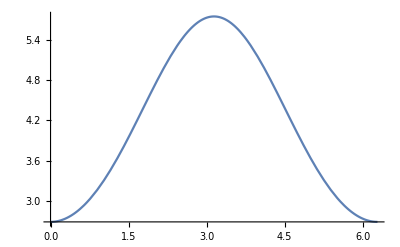

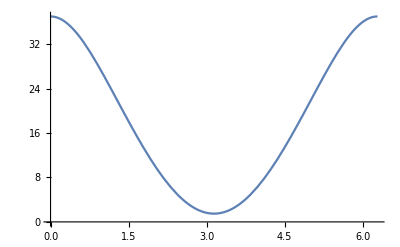

```mathematica
Plot[hampc/.point1,{ϕ,0,2π}]
Plot[AINTunpc/.point1,{ϕ,0,2π}]
```

```mathematica
(*Coefficients involving light-cone vectors*)
```

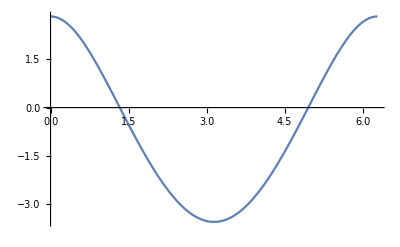

```mathematica
Plot[CINTunpc/.ξsub/.{α->1,β->1}/.point1,{ϕ,0,2π}]
```

## Convert the expression

```mathematica
(*Coefficients involving no light-cone vectors*)
```

```mathematica
hampc//Variables
```

{M,Q,t,xB,y,Cos[ϕ]}

```mathematica
hampc// CForm
```

(-4*(-0.125*(Power(Q,2)*Power(-Power(Q,2) - t,2)) + (Power(Q,2)*(-Power(Q,2) - t)*
          (Power(Q,2)/2. + (-Power(Q,2) - t)/2. + (Power(Q,2)*(1 - y))/(2.*xB*y) + 
            (Power(Q,2)*(-1 + y)*(M - t/(2.*M) - Sqrt(t*(-1 + t/(4.*Power(M,2))))*
                  (((2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*(-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                     (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)) + 
                    (2*(Power(Q,2) + t*xB)*Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/
                          (1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*Cos(ϕ))/
                     (Q*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(-1 + y)))))/(2.*M*xB*y)))/2. - 
       Power(Q,2)*Power(Power(Q,2)/2. + (-Power(Q,2) - t)/2. + (Power(Q,2)*(1 - y))/(2.*xB*y) + 
          (Power(Q,2)*(-1 + y)*(M - t/(2.*M) - Sqrt(t*(-1 + t/(4.*Power(M,2))))*
                (((2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*(-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                   (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)) + 
                  (2*(Power(Q,2) + t*xB)*Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/
                        (1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*Cos(ϕ))/
                   (Q*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(-1 + y)))))/(2.*M*xB*y),2)))/Power(-Power(Q,2) - t,2)

```mathematica
(*Coefficients involving light-cone vectors*)
```

```mathematica
BINTunpc/.ξsub//Variables
```

{M,Q,t,xB,y,α,β,Cos[ϕ]}

```mathematica
BINTunpc/.ξsub//CForm
```

(8*t*(-2*(-Power(Q,2) - t)*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
          (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
               t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
             (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
           (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                (-1 + 2*β),2)))*Power(Power(Q,2)/2. + (-Power(Q,2) - t)/2. + (Power(Q,2)*(1 - y))/(2.*xB*y) + 
          (Power(Q,2)*(-1 + y)*(M - t/(2.*M) - Sqrt(t*(-1 + t/(4.*Power(M,2))))*
                (((2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*(-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                   (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)) + 
                  (2*(Power(Q,2) + t*xB)*Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/
                        (1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*Cos(ϕ))/
                   (Q*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(-1 + y)))))/(2.*M*xB*y),3) - 
       Power(Power(Q,2)/2. + (-Power(Q,2) - t)/2. + (Power(Q,2)*(1 - y))/(2.*xB*y) + 
          (Power(Q,2)*(-1 + y)*(M - t/(2.*M) - Sqrt(t*(-1 + t/(4.*Power(M,2))))*
                (((2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*(-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                   (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)) + 
                  (2*(Power(Q,2) + t*xB)*Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/
                        (1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*Cos(ϕ))/
                   (Q*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(-1 + y)))))/(2.*M*xB*y),2)*
        (((-Power(Q,2) - t)*Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                  (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
               t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
             (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
           Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2) + 
          ((-Power(Q,2) - t)*((-2*Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                       (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                    t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                  (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)\
                - 2*(-2*Power(Q,2) - t)*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + (Power(α,2)*
                     (t + 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                       t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                     (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                   (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))))/2. - 
          2*(-0.5*(Power(Q,2)*(-Power(Q,2) - t)) - Power(-Power(Q,2) - t,2)/4.)*
           (-2*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
                (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                         (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                     t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                   (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                 (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                      (-1 + 2*β),2))) - (-((Power(Q,2)*(-1 + y)*(M - t/(2.*M) - 
                       (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*(-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                        (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*(-1 + α)*
                     (1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β)))/M
                   ) + Power(Q,2)*(1 - α + y*(-1 + xB + α))*(1 + (xB/(2 - xB) - 
                      (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β)) - 
                (2*Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                        (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/(M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*α*
                   (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                   (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                          4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                              (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                      Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                         (-1 + 2*β),2)))/M + 2*Power(Q,2)*(-1 + y)*α*(xB/(2 - xB) - 
                   (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*β*
                 (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),
                            2)) - 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                            (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                    Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                       (-1 + 2*β),2)) + (2*Q*Sqrt(t*(-1 + t/(4.*Power(M,2))))*(Power(Q,2) + t*xB)*
                   Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*
                   Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*
                   ((-1 + α)*(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                         (-1 + 2*β)) + 2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                         (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                      (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                             4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                 (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                         Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                            (-1 + 2*β),2)))*Cos(ϕ))/(M*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))))/
              (2.*xB*y*((2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                     (Power(M,2) + t*(-1 + β)*β)*(-1 + (α*(t*(-1 + Power(xB/(2 - xB) - 
                                 (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                            4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                        Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                           (-1 + 2*β),2)))/
                   (2 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-2 + 4*β)) - 
                  ((1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β))*
                     (((1 - α)*(t + (t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                               4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))/
                             Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                                (-1 + 2*β),2)))/
                        (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))) - 
                       (-Power(Q,2) + (Power(-1 + α,2)*(t*(-1 + Power(xB/(2 - xB) - 
                                    (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                               4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                           Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                              (-1 + 2*β),2))/
                        (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
                          (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                                  (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                               t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))
                              *(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                           Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                              (-1 + 2*β),2))))/4.)))) + (Power(Q,2)*(-Power(Q,2) - t)*
          (((-Power(Q,2) - t)*Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                    (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                 t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
               (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
             (2.*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),
                2)) - (Power(-Power(Q,2) - t,2)*(-2*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + (Power(α,2)*
                       (t + 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                             (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                         t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                       (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                     (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                             (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))) - 
                 (-((Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                              (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/(M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*
                         (-1 + α)*(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                            (-1 + 2*β)))/M) + Power(Q,2)*(1 - α + y*(-1 + xB + α))*
                     (1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β)) - 
                    (2*Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                            (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/(M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*α*
                       (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                       (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                    (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                              4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                  (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                          Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                             (-1 + 2*β),2)))/M + 2*Power(Q,2)*(-1 + y)*α*
                     (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*β*
                     (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                  (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                            4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                        Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                           (-1 + 2*β),2)) + (2*Q*Sqrt(t*(-1 + t/(4.*Power(M,2))))*(Power(Q,2) + t*xB)*
                       Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*
                       Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*
                       ((-1 + α)*(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                             (-1 + 2*β)) + 2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                             (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                          (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                             Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))*Cos(ϕ))/
                     (M*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))))/
                  (2.*xB*y*((2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                         (Power(M,2) + t*(-1 + β)*β)*(-1 + (α*(t*(-1 + Power(xB/(2 - xB) - 
                                     (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                    (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                            Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                               (-1 + 2*β),2)))/
                       (2 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-2 + 4*β))\
                       - ((1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                            (-1 + 2*β))*(((1 - α)*(t + (t*(-1 + Power(xB/(2 - xB) - 
                                        (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                   4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))/
                                 Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))/
                            (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))) - 
                           (-Power(Q,2) + (Power(-1 + α,2)*(t*(-1 + Power(xB/(2 - xB) - 
                                        (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                   4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                               Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))/
                            (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
                              (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                                      (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                                   t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                                 (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                               Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))))/4.))))/4.))/4. + 
       (Power(Q,2)/2. + (-Power(Q,2) - t)/2. + (Power(Q,2)*(1 - y))/(2.*xB*y) + 
          (Power(Q,2)*(-1 + y)*(M - t/(2.*M) - Sqrt(t*(-1 + t/(4.*Power(M,2))))*
                (((2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*(-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                   (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)) + 
                  (2*(Power(Q,2) + t*xB)*Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/
                        (1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*Cos(ϕ))/
                   (Q*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(-1 + y)))))/(2.*M*xB*y))*
        (-0.5*(Power(-Power(Q,2) - t,2)*Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                   (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
              (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
            Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2) + 
          (Power(Q,2)*Power(-Power(Q,2) - t,2)*(-2*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + (Power(α,2)*
                     (t + 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                       t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                     (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                   (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))) - 
               (-((Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                            (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/(M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*
                       (-1 + α)*(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                          (-1 + 2*β)))/M) + Power(Q,2)*(1 - α + y*(-1 + xB + α))*
                   (1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β)) - 
                  (2*Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                          (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/(M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*α*
                     (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                     (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                  (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                            4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                        Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                           (-1 + 2*β),2)))/M + 2*Power(Q,2)*(-1 + y)*α*(xB/(2 - xB) - 
                     (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*β*
                   (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                          4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                              (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                      Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                         (-1 + 2*β),2)) + (2*Q*Sqrt(t*(-1 + t/(4.*Power(M,2))))*(Power(Q,2) + t*xB)*
                     Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*
                     Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*
                     ((-1 + α)*(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                           (-1 + 2*β)) + 2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                        (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                               4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                           Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                              (-1 + 2*β),2)))*Cos(ϕ))/(M*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))))/
                (2.*xB*y*((2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                       (Power(M,2) + t*(-1 + β)*β)*(-1 + (α*(t*(-1 + Power(xB/(2 - xB) - 
                                   (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                              4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                  (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                          Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                             (-1 + 2*β),2)))/
                     (2 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-2 + 4*β)) - 
                    ((1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β))*
                       (((1 - α)*(t + (t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))/
                               Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))/
                          (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))) - 
                         (-Power(Q,2) + (Power(-1 + α,2)*(t*(-1 + Power(xB/(2 - xB) - 
                                      (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                             Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                                (-1 + 2*β),2))/
                          (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
                            (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                                    (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                                 t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),
                                   2))*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                             Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))))/4.))))/4. + 
          (Power(-Power(Q,2) - t,3)*(-2*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + (Power(α,2)*
                     (t + 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                       t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                     (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                   (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))) - 
               (-((Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                            (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/(M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*
                       (-1 + α)*(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                          (-1 + 2*β)))/M) + Power(Q,2)*(1 - α + y*(-1 + xB + α))*
                   (1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β)) - 
                  (2*Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                          (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/(M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*α*
                     (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                     (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                  (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                            4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                        Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                           (-1 + 2*β),2)))/M + 2*Power(Q,2)*(-1 + y)*α*(xB/(2 - xB) - 
                     (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*β*
                   (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                          4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                              (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                      Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                         (-1 + 2*β),2)) + (2*Q*Sqrt(t*(-1 + t/(4.*Power(M,2))))*(Power(Q,2) + t*xB)*
                     Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*
                     Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*
                     ((-1 + α)*(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                           (-1 + 2*β)) + 2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                        (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                               4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                           Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                              (-1 + 2*β),2)))*Cos(ϕ))/(M*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))))/
                (2.*xB*y*((2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                       (Power(M,2) + t*(-1 + β)*β)*(-1 + (α*(t*(-1 + Power(xB/(2 - xB) - 
                                   (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                              4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                  (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                          Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                             (-1 + 2*β),2)))/
                     (2 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-2 + 4*β)) - 
                    ((1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β))*
                       (((1 - α)*(t + (t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))/
                               Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))/
                          (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))) - 
                         (-Power(Q,2) + (Power(-1 + α,2)*(t*(-1 + Power(xB/(2 - xB) - 
                                      (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                             Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                                (-1 + 2*β),2))/
                          (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
                            (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                                    (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                                 t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),
                                   2))*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                             Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))))/4.))))/4. - 
          (Power(Q,2)*((-2*(-0.5*(Power(Q,2)*(-Power(Q,2) - t)) + Power(-Power(Q,2) - t,2)/2.)*Power(α,2)*
                  (t + 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),
                      2) - t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                  (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                     (-1 + 2*β),2)) - (Power(-Power(Q,2) - t,2)*(xB/(2 - xB) - 
                    (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
                    (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                             (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                         t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                       (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                     (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                             (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))))/2. - 
               (Power(-Power(Q,2) - t,2)*(-2*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                        (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
                       (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                               (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                            t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                          (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                        (Power(Q,2)*Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))) - 
                    (-((Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                                 (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                               (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))*(-1 + α)*
                            (1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                               (-1 + 2*β)))/M) + Power(Q,2)*(1 - α + y*(-1 + xB + α))*
                        (1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β))
                         - (2*Power(Q,2)*(-1 + y)*(M - t/(2.*M) - (Sqrt(t*(-1 + t/(4.*Power(M,2))))*(2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*
                               (-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/(M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)))
                           *α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + β)*
                          (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                 4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                             Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))/M + 
                       2*Power(Q,2)*(-1 + y)*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                           (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*β*
                        (-1 + (α*(t*(-1 + Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                               4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                           Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                              (-1 + 2*β),2)) + (2*Q*Sqrt(t*(-1 + t/(4.*Power(M,2))))*(Power(Q,2) + t*xB)*
                          Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*
                          Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*
                          ((-1 + α)*(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                   (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β)) + 
                            2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                             (-1 + β)*(-1 + (α*(t*(-1 + Power(xB/(2 - xB) - 
                                         (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                    4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                        (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                                Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                      (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))*Cos(ϕ))/
                        (M*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))))/
                     (2.*xB*y*((2*α*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                            (Power(M,2) + t*(-1 + β)*β)*(-1 + (α*(t*(-1 + 
                                      Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                         (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                   4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                       (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                               Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                     (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))/
                          (2 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*
                             (-2 + 4*β)) - ((1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                  (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β))*
                            (((1 - α)*(t + (t*(-1 + Power(xB/(2 - xB) - 
                                           (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                      4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                          (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))/
                                    Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                          (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2)))/
                               (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))) - 
                              (-Power(Q,2) + (Power(-1 + α,2)*(t*(-1 + Power(xB/(2 - xB) - 
                                           (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)) - 
                                      4*Power(M,2)*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                          (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2)))/
                                  Power(1 + (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                        (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))/
                               (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))) + 
                                 (Power(α,2)*(t + 4*Power(M,2)*Power(xB/(2 - xB) - 
                                         (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2) - 
                                      t*Power(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                          (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))),2))*
                                    (xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/(Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β)))))/
                                  Power(Q + Q*(xB/(2 - xB) - (2*xB*(2*Power(M,2)*Power(xB,2)*α + t*(-1 + xB)*(1 - 2*α + xB*(-1 + β))))/
                                        (Power(Q,2)*Power(-2 + xB,2)*(1 + xB*(-1 + β))))*(-1 + 2*β),2))))/4.))))/2.))/2.)))/
   (Power(-Power(Q,2) - t,2)*(Power(Q,2)/2. + (-Power(Q,2) - t)/2. + (Power(Q,2)*(1 - y))/(2.*xB*y) + 
       (Power(Q,2)*(-1 + y)*(M - t/(2.*M) - Sqrt(t*(-1 + t/(4.*Power(M,2))))*
             (((2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*(-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)) + 
               (2*(Power(Q,2) + t*xB)*Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/
                     (1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*Cos(ϕ))/
                (Q*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(-1 + y)))))/(2.*M*xB*y))*
     (Power(Q,2)/2. + (-Power(Q,2) - t)/2. + (Power(Q,2) + t)/2. + (Power(Q,2)*(1 - y))/(2.*xB*y) + 
       (Power(Q,2)*(-1 + y)*(M - t/(2.*M) - Sqrt(t*(-1 + t/(4.*Power(M,2))))*
             (((2*Power(M,2)*t*xB + Power(Q,2)*(t - 2*Power(M,2)*xB))*(-1 + y + (2*Power(M,2)*Power(xB,2)*y)/Power(Q,2)))/
                (M*Power(Q,2)*Sqrt(t*(-4 + t/Power(M,2)))*(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(1 - y)) + 
               (2*(Power(Q,2) + t*xB)*Sqrt(1 - Power(1 + (2*Power(M,2)*(Power(Q,2) + t)*Power(xB,2))/(Power(Q,4) + Power(Q,2)*t*xB),2)/
                     (1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2)))*Sqrt(1 - y - (Power(M,2)*Power(xB,2)*Power(y,2))/Power(Q,2))*Cos(ϕ))/
                (Q*Sqrt(t*(-4 + t/Power(M,2)))*Sqrt(1 + (4*Power(M,2)*Power(xB,2))/Power(Q,2))*(-1 + y)))))/(2.*M*xB*y)))